# Expected probability of infection

To test whether or not our expression for the probability of co-location (and infection, if temperature-dependent transmission is equal to 1) matched simulated values for each of our different assumptions, we simulated all of them across a range of values.

## Uniform distribution

If we assume that the expectation of our simulation can be given by a known distribution or by just constant values, we can then calculate our expected values and test whether or not they align with what the simulated values show.

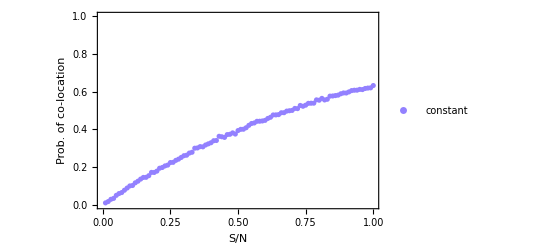

```mathematica
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];

Np=100; (* Number of Patches *) 
NI=1; (* Number of Infected Individuals *)

reps=10000; (* Replications to do for each parameter set *)

(* This counts the fraction of successes -- colacations of infected and susceptible indivdiuals in each trial, across a range of the number of susceptibles *)

(* The result is invariant when expressed as a ratio of S/N -- number of susceptibles per number of patches *)

output=ParallelTable[Module[{success},
success=0;
Do[
weights=ConstantArray[1,Np];
Sloc=RandomChoice[weights->Range[1,Np,1],NS];
Iloc=RandomChoice[weights->Range[1,Np,1],NI];
If[Length[Intersection[Sloc,Iloc]]>0,success++],{reps}];
{NS/Np,N[success/reps]}],{NS,1,Np}];
(* I want points that have a border so they're easier to see*)
plot1=ListPlot[{output},Frame->{True,True,False,False},
	PlotRange->{0,1},
	PlotStyle->{RGBColor["#9381ff"], Opacity[0.1]}, 
	FrameLabel->{"S/N","Prob. of co-location"},
	PlotLegends->{"constant "}]
```

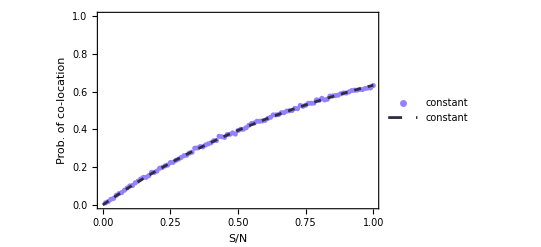

```mathematica
(* Add the expected value of this based on the math*)
expectation=ParallelTable[{NS/Np,N[1-(1-(1/Np))^NS]},{NS,0,Np}];
plot2=Show[
	plot1,
	ListLinePlot[expectation,
		PlotStyle->{RGBColor["#2b2d42"],Dashed},
		PlotLegends->{"constant "}]]
		
Export[relativePath["figs/si","constant-expected.pdf"],plot2, 
	ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

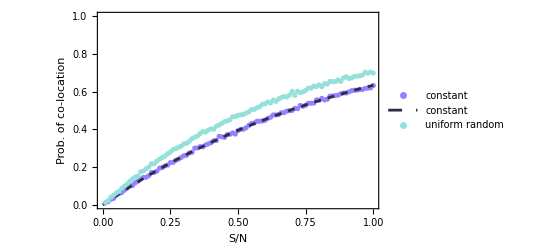

```mathematica
(*Now try it with random weights from a uniform distirbution *)
output=ParallelTable[Module[{success},
success=0;
Do[
weights=RandomReal[UniformDistribution[],Np];
Sloc=RandomChoice[weights->Range[1,Np,1],NS];
Iloc=RandomChoice[weights->Range[1,Np,1],NI];
If[Length[Intersection[Sloc,Iloc]]>0,success++],{reps}];
{NS/Np,N[success/reps]}],{NS,1,Np}];

plot3=Show[plot2,
	plotrnun=ListPlot[{output},Frame->{True,True,False,False},
	PlotStyle->RGBColor["#93e1d8"],
	FrameLabel->{"S/N","Prob. of co-location"},
	PlotLegends->{"uniform random "}]]
```

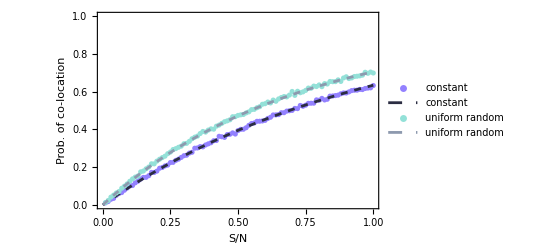

```mathematica
(* Add the expected value of this based on the math*)
weights=RandomReal[{0,1},Np]; (* Get a vector of random values *)
weights=weights/Total[weights]; (* Turn them into propoer weights *)

(* The expression below can be slightly simplified, but only by multiplying the two terms out an collecting terms *) 
expectation2=ParallelTable[{NS/Np,Sum[(1-(1-weights[[i]])^NS ) (1-(1-weights[[i]])^NI),{i,1,Np}]},{NS,0,Np}];

plot4=Show[plot3,
	ListLinePlot[expectation2,
		PlotStyle->{RGBColor["#8d99ae"],Dashed},
		PlotLegends->{"uniform random "}]]
Export[relativePath["figs/si","constant-uniform.pdf"],plot4, 
	ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

(1-p^2+S-ⅇ^-p (-p)^-S (1+p+S) ((-1+(-1)^(2 S)) Gamma[2+S]+Gamma[2+S,-p]))/(1+S)

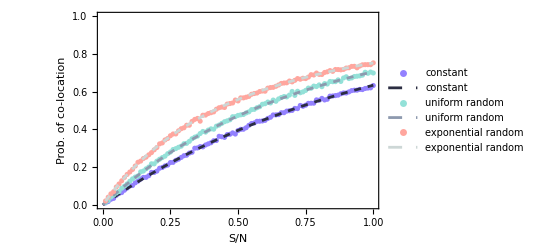

```mathematica
Assuming[{p>2,S>=1},Expectation[p*w(1-(1-w)^S ),w\[Distributed]ExponentialDistribution[p]]];
solution=FullSimplify[%]

output=ParallelTable[Module[{success},
success=0;
Do[
weights=RandomReal[ExponentialDistribution[Np],Np];
Sloc=RandomChoice[weights->Range[1,Np,1],NS];
Iloc=RandomChoice[weights->Range[1,Np,1],NI];
If[Length[Intersection[Sloc,Iloc]]>0,success++],{reps}];
{NS/Np,N[success/reps]}],{NS,1,Np}];

(*Show[plot4,plotrnexp=ListPlot[{output},Frame->{True,True,False,False},PlotStyle->ColorData[97,5],FrameLabel->{"S/N","Prob. of encounter"},PlotLegends->{"Weights=Exponential Random"}]]*)
plot5=Show[plot4, 
	ListPlot[{output},Frame->{True,True,False,False},
		PlotStyle->RGBColor["#ffa69e"],FrameLabel->{"S/N","Prob. of encounter"},
		PlotLegends->{"exponential random "}], 
	ListLinePlot[Table[{S/Np,solution/.p->Np},{S,1,Np}],
		PlotStyle->{Dashed,RGBColor["#cdd7d6"]},
		PlotLegends->{"exponential random "}]]
Export[relativePath["figs/si","constant-uni-exp.pdf"],plot5, 
	ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```